```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
$FAVerbose=0;
```

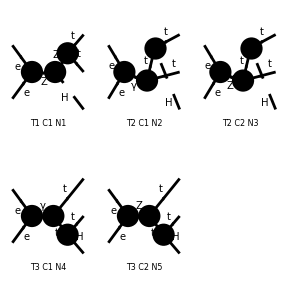

(e m_W (ḡ)^Lor1Lor2 (ḡ)^Lor2Lor4 (ḡ)^Lor3Lor4 (φ(-OverBar[p2],m_e)).((ⅈ e (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(ⅈ e (γ̄)^Lor1.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p1],m_e)) (φ(OverBar[k1],m_t)).((ⅈ e (γ̄)^Lor3.(γ̄)^7 δ_Col3Col4 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(2 ⅈ e (γ̄)^Lor3.(γ̄)^6 δ_Col3Col4 (sin(θ_W)))/(3 (cos(θ_W)))).(φ(-OverBar[k2],m_t)))/((cos(θ_W))^2 (sin(θ_W)) ((-OverBar[k1]-OverBar[k2])^2-m_Z^2) ((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))

(ⅈ (ḡ)^Lor1Lor2 (φ(-OverBar[p2],m_e)).((ⅈ e (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(ⅈ e (γ̄)^Lor1.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p1],m_e)) (φ(OverBar[k1],m_t)).((ⅈ e (γ̄)^Lor2.(γ̄)^7 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(2 ⅈ e (γ̄)^Lor2.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))).(γ̄·(-OverBar[k2]-OverBar[k3])+m_t).(-(ⅈ e m_t δ_Col3Col4)/(2 m_W (sin(θ_W)))).(φ(-OverBar[k2],m_t)))/(((OverBar[k2]+OverBar[k3])^2-m_t^2) ((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))

(ⅈ (ḡ)^Lor1Lor2 (φ(-OverBar[p2],m_e)).((ⅈ e (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(ⅈ e (γ̄)^Lor1.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p1],m_e)) (φ(OverBar[k1],m_t)).(-(ⅈ e m_t)/(2 m_W (sin(θ_W)))).(γ̄·(OverBar[k1]+OverBar[k3])+m_t).((ⅈ e (γ̄)^Lor2.(γ̄)^7 δ_Col3Col4 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(2 ⅈ e (γ̄)^Lor2.(γ̄)^6 δ_Col3Col4 (sin(θ_W)))/(3 (cos(θ_W)))).(φ(-OverBar[k2],m_t)))/(((-OverBar[k1]-OverBar[k3])^2-m_t^2) ((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))

(ⅈ (ḡ)^Lor1Lor2 (φ(-OverBar[p2],m_e)).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p1],m_e)) (φ(OverBar[k1],m_t)).(-2/3 ⅈ e (γ̄)^Lor2).(γ̄·(-OverBar[k2]-OverBar[k3])+m_t).(-(ⅈ e m_t δ_Col3Col4)/(2 m_W (sin(θ_W)))).(φ(-OverBar[k2],m_t)))/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2 ((OverBar[k2]+OverBar[k3])^2-m_t^2))

(ⅈ (ḡ)^Lor1Lor2 (φ(-OverBar[p2],m_e)).(ⅈ e (γ̄)^Lor1).(φ(OverBar[p1],m_e)) (φ(OverBar[k1],m_t)).(-(ⅈ e m_t)/(2 m_W (sin(θ_W)))).(γ̄·(OverBar[k1]+OverBar[k3])+m_t).(-2/3 ⅈ e (γ̄)^Lor2 δ_Col3Col4).(φ(-OverBar[k2],m_t)))/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2 ((-OverBar[k1]-OverBar[k3])^2-m_t^2))

```mathematica
SetOptions[InitializeModel,ModelEdit:>(M$ClassesDescription=M$ClassesDescription/.MZ->MZc)];
InitializeModel[{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];

NoElectronHCoupling=ExcludeFieldPoints->{FieldPoint[0][-F[2,{1}],F[1,{1}],S[3]],FieldPoint[0][-F[2,{1}],F[2,{1}],S[1]],FieldPoint[0][-F[2,{1}],F[2,{1}],S[2]]};

part=InsertFields[CreateTopologies[0,2->3],{F[2,{1}],-F[2,{1}]}->{F[3,{3}],-F[3,{3}],S[1]},Restrictions->NoElectronHCoupling,InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
Paint[part,PaintLevel->{Classes}];

listdiag=FCFAConvert[CreateFeynAmp[part],SMP->True,ChangeDimension->4,IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2,k3},DropSumOver->True,List->False,UndoChiralSplittings->True];
diag1=listdiag[[5]]
diag2=listdiag[[4]]
diag3=listdiag[[3]]
diag4=listdiag[[2]]
diag5=listdiag[[1]]
```

```mathematica
ClearScalarProducts;

SP[p1,p1]=me^2;
SP[p2,p2]=me^2;
SP[p1,p2]=(s-2 me^2)/2;

SP[k1,k1]=mt^2;
SP[k2,k2]=mt^2;
SP[k3,k3]=mh^2;
SP[k1,k2]=(s3-2 mt^2)/2;
SP[k1,k3]=(s2-mt^2-mh^2)/2;
SP[k2,k3]=(s1-mt^2-mh^2)/2;

diag1=diag1/.{Lor1->μ,Lor2->ν,Lor3->α,Lor4->β};
diag1C=ComplexConjugate[diag1]/.{μ->μlin,ν->νlin,α->αlin,β->βlin};
```

```mathematica
M12=diag1 diag1C//Contract
```

1/((cos(θ_W))^4 (sin(θ_W))^2)e^2 m_W^2 (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (φ(-OverBar[p2],m_e)).((ⅈ e (γ̄)^μ.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(ⅈ e (γ̄)^μ.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p1],m_e)) (φ(OverBar[p1],m_e)).(-(ⅈ e (γ̄)^7.(γ̄)^μlin (sin(θ_W)))/(cos(θ_W))-(ⅈ e (γ̄)^6.(γ̄)^μlin ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[p2],m_e)) (φ(OverBar[k1],m_t)).((ⅈ e (γ̄)^μ.(γ̄)^7 δ_Col3Col4 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(2 ⅈ e (γ̄)^μ.(γ̄)^6 δ_Col3Col4 (sin(θ_W)))/(3 (cos(θ_W)))).(φ(-OverBar[k2],m_t)) (φ(-OverBar[k2],m_t)).((2 ⅈ e (γ̄)^7.(γ̄)^μlin δ_Col3Col4 (sin(θ_W)))/(3 (cos(θ_W)))-(ⅈ e (γ̄)^6.(γ̄)^μlin δ_Col3Col4 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[k1],m_t))

```mathematica
res=((M12//FermionSpinSum)/.DiracTrace->Tr)//Contract;
```

```mathematica
FreeQ2[res,{DiracTrace,LorentzIndex}]
```

True

```mathematica
res
```

(320 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(160 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/(9 (cos(θ_W))^8)+(80 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(320 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_t^2 m_W^2 e^6)/(9 (cos(θ_W))^8)+(320 me^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(160 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(9 (cos(θ_W))^8)+(80 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(320 me^2 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)+(160 mt^2 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(80 mt^2 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)+(160 me^2 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(80 s s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)+(40 (s-2 me^2) s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(80 me^2 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)+(40 s (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8)-(160 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1]) m_W^2 e^6)/(9 (cos(θ_W))^8)-(160 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]) m_W^2 e^6)/(9 (cos(θ_W))^8)-(256 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(128 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(64 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(256 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_t^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(256 me^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(128 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(64 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(256 me^2 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(128 mt^2 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(64 mt^2 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(128 me^2 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(64 s s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(32 (s-2 me^2) s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(64 me^2 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(32 s (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(128 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1]) m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)+(128 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]) m_W^2 (sin(θ_W))^2 e^6)/(9 (cos(θ_W))^8)-(56 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^2)+(28 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^2)-(14 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^2)+(32 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_t^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^2)-(128 me^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(64 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)-(32 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(200 me^2 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)-(100 mt^2 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(50 mt^2 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)-(100 me^2 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(50 s s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)-(25 (s-2 me^2) s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(50 me^2 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)-(25 s (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(100 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1]) m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(100 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]) m_W^2 e^6)/(9 (cos(θ_W))^8 (sin(θ_W))^2)+(8 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])-2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])) m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^2)+(4 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/((cos(θ_W))^8 (sin(θ_W))^4)-(2 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/((cos(θ_W))^8 (sin(θ_W))^4)+((s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_e^2 m_W^2 e^6)/((cos(θ_W))^8 (sin(θ_W))^4)+(8 me^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)-(4 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)+(2 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_t^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)-(20 me^2 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)+(10 mt^2 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)-(5 mt^2 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)+(10 me^2 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)-(5 s s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)+(5 (s-2 me^2) s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(6 (cos(θ_W))^8 (sin(θ_W))^4)-(5 me^2 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)+(5 s (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(6 (cos(θ_W))^8 (sin(θ_W))^4)-(10 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1]) m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)-(10 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]) m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)-(5 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])-2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])) m_W^2 e^6)/(3 (cos(θ_W))^8 (sin(θ_W))^4)+(me^2 mt^2 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/((cos(θ_W))^8 (sin(θ_W))^6)-(mt^2 s N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(2 (cos(θ_W))^8 (sin(θ_W))^6)+(mt^2 (s-2 me^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(4 (cos(θ_W))^8 (sin(θ_W))^6)-(me^2 s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(2 (cos(θ_W))^8 (sin(θ_W))^6)+(s s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(4 (cos(θ_W))^8 (sin(θ_W))^6)-((s-2 me^2) s3 N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(8 (cos(θ_W))^8 (sin(θ_W))^6)+(me^2 (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(4 (cos(θ_W))^8 (sin(θ_W))^6)-(s (s3-2 mt^2) N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 m_W^2 e^6)/(8 (cos(θ_W))^8 (sin(θ_W))^6)+(N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1]) m_W^2 e^6)/(2 (cos(θ_W))^8 (sin(θ_W))^6)+(N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]) m_W^2 e^6)/(2 (cos(θ_W))^8 (sin(θ_W))^6)+(N (1/((-OverBar[k1]-OverBar[k2])^2-m_Z^2))^2 (1/((OverBar[k1]+OverBar[k2]+OverBar[k3])^2-m_Z^2))^2 (2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])-2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])) m_W^2 e^6)/(4 (cos(θ_W))^8 (sin(θ_W))^6)